## Figure 2 and 3 (Two species which only differ in soil and resource preference)

### Setup

```mathematica
ClearAll["α","f"]
```

```mathematica
f[ν_,σ_,ζ_]:=ν NIntegrate[Exp[-x^2/σ^2]Exp[(-(x-ζ)^4)/(81 σ^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^4/ω^4-(Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^4/ω^4-(α Subscript[N, 1]+Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Equilibrium

```mathematica
eqN=FullSimplify[Solve[Subscript[dN, 1]==0&&Subscript[dN, 2]==0,{Subscript[N, 1],Subscript[N, 2]}]]
```

{{N_1→0,N_2→0},{N_1→0,N_2→1-(S-ϵ)^4/ω^4},{N_1→(-S^4 (-1+α)+4 S^3 α ϵ-6 S^2 α ϵ^2+4 S α ϵ^3-α ϵ^4+(-1+α) ω^4)/((-1+α^2) ω^4),N_2→(-S^4 (-1+α)-4 S^3 ϵ+6 S^2 ϵ^2-4 S ϵ^3+ϵ^4+(-1+α) ω^4)/((-1+α^2) ω^4)},{N_1→1-S^4/ω^4,N_2→0}}

### Figure 2a (Coexistence and priority effects with PSF)

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Do[
ch1=0;
ch2=0;
Do[
α=f[ν/.pars,σ/.pars,ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]];

eqCounts[[Length[eq[[j1,j2]]]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,4113,0,523,0,0}

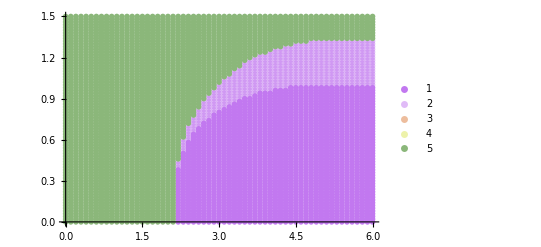

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

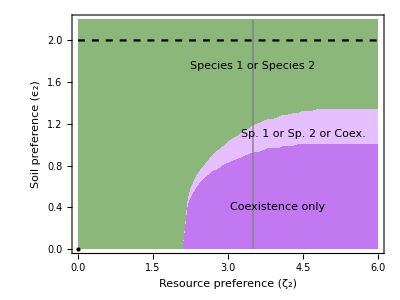

```mathematica
fig2a=Show[{RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,6},{y,0,2.2},PlotStyle->{{ColorData[95,0],Opacity[1]},{RGBColor[0.9,0.75,1,0.99]},{ColorData["Pastel",0],Opacity[1]}},BoundaryStyle->None],Plot[2ω/.pars,{ζ,0,6},PlotStyle->{Dashed,Black}]},Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{Gray,Line[{{3.5,0},{3.5,2.2}}]},{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->13]],{3.5,1.75}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->13]],{4.5,1.1}],Inset[Text[Style["Coexistence only ",FontSize->13]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig2a.pdf",fig2a];
```

```mathematica
ζs[[36]]
```

3.5

```mathematica
ϵ1Fix=z1[[36,2]]
ϵ2Fix=z2[[36,2]]
```

0.92

1.18

### Figure 2b (PSF and competition figure with soil origin dependence)

```mathematica
pars={ω->1,σ->1,ν->1,η->1,ζ->3.5};
α=f[ν/.pars,σ/.pars,ζ/.pars]
```

0.323783

```mathematica
ϵs = Join[Range[0, 0.9, 0.1],Range[0.9,1.4,0.05], Range[1.4, 2.3, 0.1]];
nϵ = Length[ϵs];
Ss = Join[Range[-1.7, -0.4, 0.1], Range[-0.4, 1.2, 0.05], Range[1.2, 2.2, 0.1]];
nS = Length[Ss];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nS,3}];
yf=Array[,{nϵ*nS,3}];
yf1=Array[,{nϵ*nS,3}];
yf2=Array[,{nϵ*nS,3}];
yf3=Array[,{nϵ*nS,3}];
zf=Array[,{nϵ*nS,3}];
st=Array[,{nϵ*nS,3}];
```

```mathematica
x0=0.1;y0=0.1; T=1000; 
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
```

This defines Dormand and Prince coefficients to solve ODE equivalently to ode45 in MATLAB

```mathematica
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
```

```mathematica
Timing[
Do[
Do[
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==Ss[[j1]]},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
If[Extract[x[T]/.nsol,1]<-0.001||Extract[y[T]/.nsol,1]<-0.001,
Print[{(x[T]/.nsol),(y[T]/.nsol),Ss[[j1]],ϵs[[j2]]}],
xf[[(j1-1)*nϵ+j2]]=Flatten[{Ss[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{Ss[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{Ss[[j1]],ϵs[[j2]],z[T]/.nsol}];
If[Extract[x[T]/.nsol,1]>0.1&&Extract[y[T]/.nsol,1]>0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],0}];
If[Extract[x[T]/.nsol,1]>0.1&&Extract[y[T]/.nsol,1]<0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],1}];
If[Extract[x[T]/.nsol,1]<0.1&&Extract[y[T]/.nsol,1]>0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],2}];
If[Extract[x[T]/.nsol,1]<0.1&&Extract[y[T]/.nsol,1]<0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],3}];
],
{j2,nϵ}],
{j1,nS}]
]
```

{29.8281,Null}

```mathematica
figPSF1=ListDensityPlot[xf,ColorFunction->"CoffeeTones",Frame->True,FrameLabel->{"",""},LabelStyle->{FontSize->15,FontColor->Black},PlotLegends->BarLegend[Automatic,Automatic,LegendLabel->Placed["Abundance of species 1",Right,Rotate[#,90 Degree]&],LabelStyle->Directive[FontSize->15]]];
```

```mathematica
figPSF=ListDensityPlot[st,ColorFunction->"Pastel",Frame->True,FrameLabel->{"",""},LabelStyle->{FontSize->15,FontColor->Black}];
```

```mathematica
figPSF2=ListDensityPlot[yf,ColorFunction->"CoffeeTones",Frame->True,FrameLabel->{"",""},LabelStyle->{FontSize->15,FontColor->Black},PlotLegends->BarLegend[Automatic,Automatic,LegendLabel->Placed["Abundance of species 2",Right,Rotate[#,90 Degree]&],LabelStyle->Directive[FontSize->15]]];
```

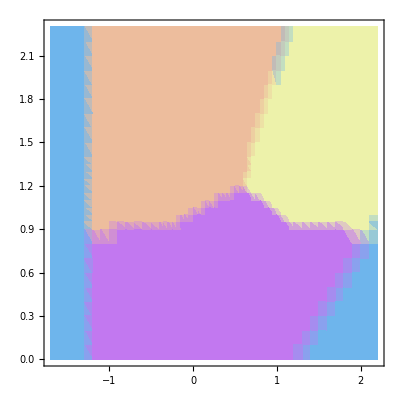

```mathematica
GraphicsRow[{figPSF1,figPSF2,figPSF},ImageSize->1000]
```

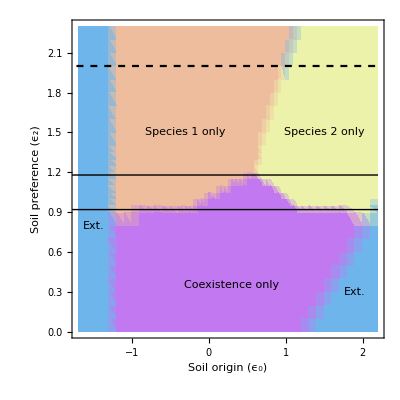

```mathematica
fig2b=Show[{figPSF,Plot[{2ω/.pars,ϵ1Fix,ϵ2Fix},{x,-1.9,2.2},PlotStyle->{{Dashed,Black},{Thin,Black},{Thin,Black}}]},Frame->True,FrameLabel->{"Soil origin (ϵ_0)","Soil preference (ϵ_2)"},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{Inset[Text[Style["Ext.",FontSize->15]],{-1.5,0.8}],Inset[Text[Style["Species 1 only",FontSize->15]],{-0.3,1.5}],Inset[Text[Style["Species 2 only",FontSize->15]],{1.5,1.5}],Inset[Text[Style["Coexistence only ",FontSize->15]],{0.3,0.35}],Inset[Text[Style["Ext.",FontSize->15]],{1.9,0.3}]}}]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig2b.jpg",fig2b,ImageResolution->500];
```

### Figure 2c (PSF and competition - allee effect, coexistence only when initial population is large)

```mathematica
pars={ω->1,σ->1,ν->1,η->1,ζ->3.5,ϵ->1};
α=f[ν/.pars,σ/.pars,ζ/.pars]
```

0.323783

```mathematica
ys=Range[0,1,0.005];
ny=Length[ys];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,ny];
yf=Array[,ny];
zf=Array[,ny];
```

```mathematica
T=1000; 
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
```

```mathematica
Timing[
Do[
nsol=NDSolve[{D[x[t],t]==dx,D[y[t],t]==dy,D[z[t],t]==dz,x[0]==1,y[0]==ys[[j]],z[0]==0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[j]]=Flatten[{ys[[j]],x[T]/.nsol}];
yf[[j]]=Flatten[{ys[[j]],y[T]/.nsol}];
zf[[j]]=Flatten[{ys[[j]],z[T]/.nsol}],
{j,ny}]
]
```

{0.59375,Null}

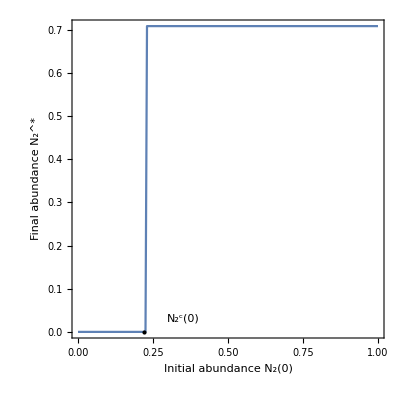

```mathematica
fig2c=ListLinePlot[yf,Frame->True,FrameLabel->{"Initial abundance N_2(0)","Final abundance N_2^*"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},AspectRatio->1,Epilog-> {{PointSize[Large],Point[{0.22,0}]},{Inset[Text[Style["N_2^c(0)",FontSize->20]],{0.35,0.03}]}}]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig2c.pdf",fig2c];
```

### Figure 2d (Allee effect - how does dissimilarity affect the allee threshold)

```mathematica
ClearAll["xf","yf","zf","pars"]
```

```mathematica
pars={ω->1,σ->1,ν->1,η->1,ζ->3.5};
α=f[ν/.pars,σ/.pars,ζ/.pars]
```

0.323783

```mathematica
ϵs=Range[0.8,1.4,0.01];
nϵ=Length[ϵs];
ys=Range[0,1.8,0.01];
ny=Length[ys];
```

```mathematica
yf=Array[,nϵ];
```

```mathematica
T=1000; 
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
```

```mathematica
Timing[
checkN=0;
j1=1;
While[checkN==0&&j1<=nϵ,
check=0;
j2=1;
While[check==0&&j2<=ny,
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j1]]),x[0]==1,y[0]==ys[[j2]],z[0]==0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
If[check==0&&Extract[y[T]/.nsol,1]>0.1,yf[[j1]]={ϵs[[j1]],ys[[j2]]};check=1];
j2=j2+1
];
If[check==0,checkN=1;ϵNul=ϵs[[j1]];yMax=yf[[j1-1,2]]];
j1=j1+1
]
]
```

{3.21875,Null}

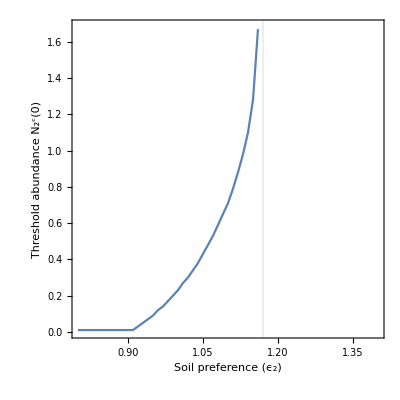

```mathematica
fig2d=ListLinePlot[yf,Frame->True,FrameLabel->{"Soil preference (ϵ_2)","Threshold abundance N_2^c(0)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},PlotRange->{{0.8,1.4},{0,1.01yMax}},GridLines->{{ϵNul},{}},AspectRatio->1]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig2d.pdf",fig2d];
```

### Figure 3a (Filtering only figure with soil origin dependence)

```mathematica
ClearAll["pars"]
pars={ω->1,σ->1,ν->1,η->1,ζ->2.5};
α=f[ν/.pars,σ/.pars,ζ/.pars]
```

0.827979

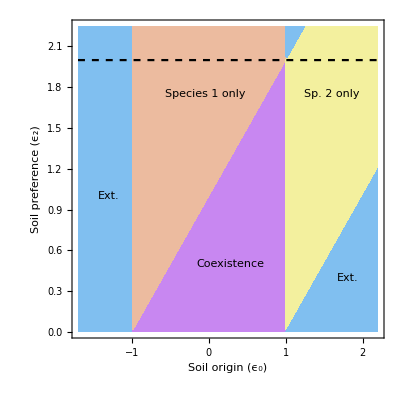

```mathematica
fig3a=Show[{RegionPlot[{S>(ϵ-ω/.pars)&&S<(ω/.pars),S<(ϵ-ω/.pars)&&(-ω/.pars)<S<(ω/.pars),S>(ω/.pars)&&S<(ϵ+ω/.pars)&&S>(ϵ-ω/.pars),S<(-ω/.pars)||S>(ϵ+ω/.pars)||(S>(ω/.pars)&&S<(ϵ-ω/.pars))},{S,-1.7,2.2},{ϵ,0,2.25},MaxRecursion->5,PlotStyle->{RGBColor[0.7859033776000001, 0.5284086576, 0.9469532752],RGBColor[0.9240375032, 0.7338094664, 0.621823488],RGBColor[0.9529226912, 0.93983914, 0.6205618136],RGBColor[0.5016764639999998, 0.7492700575999999, 0.9393325664]},BoundaryStyle->None,Frame->True,FrameLabel->{"Soil origin (ϵ_0)","Soil preference (ϵ_2)"},LabelStyle->{FontSize->20,FontColor->Black}],Plot[2ω/.pars,{S,-1.7,2.2},PlotStyle->{Dashed,Black}]},AspectRatio->1,Epilog->{Inset[Text[Style["Species 1 only ",FontSize->15]],{-0.05,1.75}],Inset[Text[Style["Coexistence ",FontSize->15]],{0.275,0.5}],Inset[Text[Style["Sp. 2 only ",FontSize->15]],{1.6,1.75}],Inset[Text[Style["Ext. ",FontSize->15]],{-1.3,1}],Inset[Text[Style["Ext. ",FontSize->15]],{1.8,0.4}]}]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig3a.pdf",fig3a];
```

### Figure 3b (Filtering and competition figure with soil origin dependence)

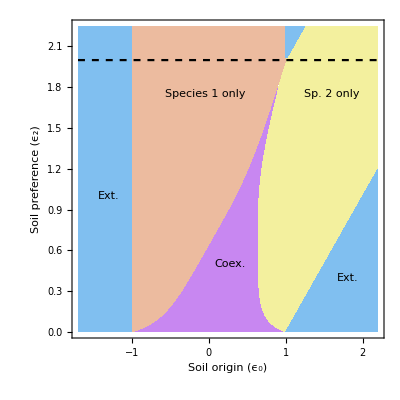

```mathematica
fig3b=Show[{RegionPlot[{((Subscript[dN, 1]/Subscript[N, 1])/.eqN[[2]]/.pars)>0&&((Subscript[dN, 2]/Subscript[N, 2])/.eqN[[4]]/.pars)>0,((Subscript[dN, 1]/Subscript[N, 1])/.eqN[[2]]/.pars)<0&&(-ω/.pars)+ϵ<S<ϵ+(ω/.pars),((Subscript[dN, 2]/Subscript[N, 2])/.eqN[[4]]/.pars)<0&&(-ω/.pars)<S<(ω/.pars),S<(-ω/.pars)||S>(ϵ+ω/.pars)||(S>(ω/.pars)&&S<(ϵ-ω/.pars))},{S,-1.7,2.2},{ϵ,0,2.25},MaxRecursion->8,PlotStyle->{RGBColor[0.7859033776000001, 0.5284086576, 0.9469532752],RGBColor[0.9529226912, 0.93983914, 0.6205618136],RGBColor[0.9240375032, 0.7338094664, 0.621823488],RGBColor[0.5016764639999998, 0.7492700575999999, 0.9393325664]},BoundaryStyle->None,Frame->True,FrameLabel->{"Soil origin (ϵ_0)","Soil preference (ϵ_2)"},LabelStyle->{FontSize->20,FontColor->Black}],Plot[2ω/.pars,{S,-1.7,2.2},PlotStyle->{Dashed,Black}]},AspectRatio->1,Epilog->{Inset[Text[Style["Species 1 only ",FontSize->15]],{-0.05,1.75}],Inset[Text[Style["Coex. ",FontSize->15]],{0.275,0.5}],Inset[Text[Style["Sp. 2 only ",FontSize->15]],{1.6,1.75}],Inset[Text[Style["Ext. ",FontSize->15]],{-1.3,1}],Inset[Text[Style["Ext. ",FontSize->15]],{1.8,0.4}]}]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig3b.pdf",fig3b];
```

### Figure 3c (PSF and competition figure with soil origin dependence)

```mathematica
ClearAll["pars"]
pars={ω->1,σ->1,ν->1,η->1,ζ->2.5};
α=f[ν/.pars,σ/.pars,ζ/.pars]
```

0.827979

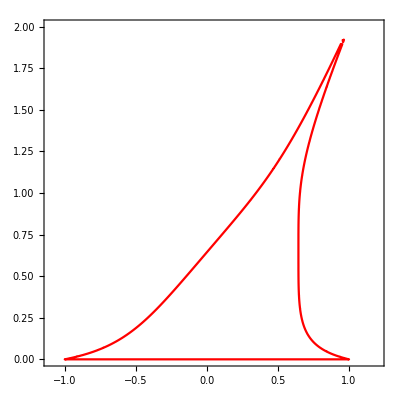

```mathematica
figCoex=RegionPlot[((Subscript[dN, 1]/Subscript[N, 1])/.eqN[[2]]/.pars)>0&&((Subscript[dN, 2]/Subscript[N, 2])/.eqN[[4]]/.pars)>0,{S,-1.1,1.2},{ϵ,0,2},MaxRecursion->8,PlotStyle->None,BoundaryStyle->Red]
```

```mathematica
ϵs = Join[Range[0, 0.5, 0.1],Range[0.5,0.9,0.01], Range[0.9, 2.3, 0.1]];
nϵ = Length[ϵs];
Ss = Join[Range[-1.7, -0.4, 0.1], Range[-0.4, 1.2, 0.01], Range[1.2, 2.2, 0.1]];
nS = Length[Ss];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nS,3}];
yf=Array[,{nϵ*nS,3}];
yf1=Array[,{nϵ*nS,3}];
yf2=Array[,{nϵ*nS,3}];
yf3=Array[,{nϵ*nS,3}];
zf=Array[,{nϵ*nS,3}];
st=Array[,{nϵ*nS,3}];
```

```mathematica
x0=0.1;y0=0.1; T=1000; 
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
```

```mathematica
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
```

```mathematica
Timing[
Do[
Do[
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==Ss[[j1]]},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
If[Extract[x[T]/.nsol,1]<-0.001||Extract[y[T]/.nsol,1]<-0.001,
Print[{(x[T]/.nsol),(y[T]/.nsol),Ss[[j1]],ϵs[[j2]]}],
xf[[(j1-1)*nϵ+j2]]=Flatten[{Ss[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{Ss[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{Ss[[j1]],ϵs[[j2]],z[T]/.nsol}];
If[Extract[x[T]/.nsol,1]>0.1&&Extract[y[T]/.nsol,1]>0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],0}];
If[Extract[x[T]/.nsol,1]>0.1&&Extract[y[T]/.nsol,1]<0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],1}];
If[Extract[x[T]/.nsol,1]<0.1&&Extract[y[T]/.nsol,1]>0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],2}];
If[Extract[x[T]/.nsol,1]<0.1&&Extract[y[T]/.nsol,1]<0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],3}];
],
{j2,nϵ}],
{j1,nS}]
]
```

{80.9219,Null}

```mathematica
figPSF=ListDensityPlot[st,ColorFunction->"Pastel",Frame->True,FrameLabel->{"",""},LabelStyle->{FontSize->15,FontColor->Black}];
```

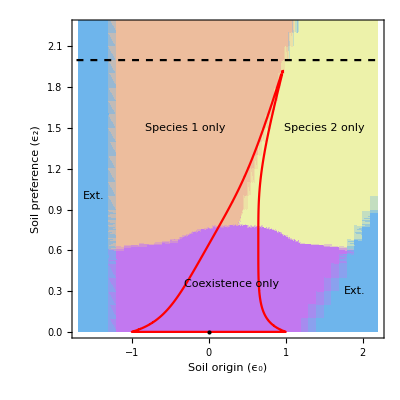

```mathematica
fig3c=Show[{figPSF,figCoex,Plot[2ω/.pars,{x,-1.9,2.2},PlotStyle->{Dashed,Black}]},Frame->True,FrameLabel->{"Soil origin (ϵ_0)","Soil preference (ϵ_2)"},LabelStyle->{FontSize->20,FontColor->Black},PlotRange->{{-1.7,2.2},{0,2.25}},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Ext.",FontSize->15]],{-1.5,1}],Inset[Text[Style["Species 1 only",FontSize->15]],{-0.3,1.5}],Inset[Text[Style["Species 2 only",FontSize->15]],{1.5,1.5}],Inset[Text[Style["Coexistence only ",FontSize->15]],{0.3,0.35}],Inset[Text[Style["Ext.",FontSize->15]],{1.9,0.3}]}}]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\fig3c.jpg",fig3c,ImageResolution->500];
```

## Numerics

```mathematica
pars={ω->1,σ->1,ν->1,η->1,ζ->2.35,ϵ->0.5};
```

```mathematica
α=f[ν/.pars,σ/.pars,ζ/.pars]
```

0.904881

```mathematica
x0=1;y0=2;z0=0; T=10000; 
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
```

```mathematica
nsol=NDSolve[{D[x[t],t]==dx,D[y[t],t]==dy,D[z[t],t]==dz,x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T}];
```

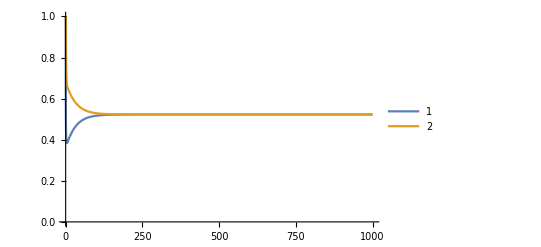

```mathematica
Plot[{x[t]/.nsol,y[t]/.nsol},{t,0,1000},PlotRange->{0,1},PlotLegends->Automatic,Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}]
```

```mathematica
eqNSol=FullSimplify[Solve[N[Subscript[dN, 1]/.pars]==0&&N[Subscript[dN, 2]/.pars]==0&&N[dS/.pars]==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{N_1→0.522917,N_2→0.522917,S→0.25}}

```mathematica
Eigenvalues[Jc/.pars/.eqNSol[[1]]]
```

{-1.06198,-0.996094,-0.033596}

```mathematica
Eigenvalues[Jc/.pars/.Subscript[N, 1]->1/.Subscript[N, 2]->0/.S->0]
```

{-1.,-1.,0.0326195}

```mathematica
Eigenvalues[Jc/.pars/.Subscript[N, 1]->0/.Subscript[N, 2]->1/.S->0.5]
```

{-1.,-1.,0.0326195}